```mathematica
ClearAll["Global`*"]
(*The objective of this is to plot the different possible orthorhombic unit cells in 2D. Experiments report a and b values. How do i get the other values from this?*)
```

2

1

1

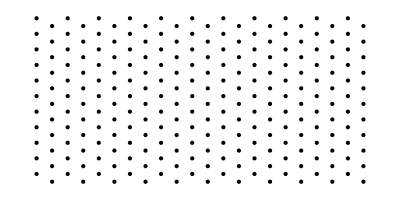

```mathematica
N1:=5 (*Max value of points to plot along each directions*)
N2:=N1
(*Here a and b corresponds to the dimensions of the unit cell shown below
-Graphics-*)
Atom1[a_,b_,r_,n2_]:=Table[{n1*a,n2*b},{n1,-N1,N1}]
Atom2[a_,b_,r_,n2_]:=Table[{n1*a-r,n2*b+b/2},{n1,-N1,N1}]
p1[a_,b_,r_]:=Atom1[a,b,r,-N2]
For[j=-N2+1,j<=N2,j++,p1[a_,b_,r_]=Join[p1[a,b,r],Atom1[a,b,r,j]]]
p2[a_,b_,r_]:=Atom2[a,b,r,-N2]
For[j=-N2+1,j<=N2,j++,p2[a_,b_,r_]=Join[p2[a,b,r],Atom2[a,b,r,j]]]
Manipulate[Graphics[{Point[p1[a,b,r]],Point[p2[a,b,r]]}],{{r,a/2},0,a},{{b,1},0,1},{{a,2},1,2}]
a1=2
b1=1
r1=a1/2
Graphics[{Point[p1[a1,b1,r1]],Point[p2[a1,b1,r1]]}]
```

```mathematica
(*Rough Work*)
```

-Graphics-

-Graphics-

{{0,jj},{1,jj},{2,jj},{3,jj},{4,jj},{5,jj}}

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0}}

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{0,1},{1,1},{2,1},{3,1},{4,1},{5,1}}

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{0,1},{1,1},{2,1},{3,1},{4,1},{5,1},{0,2},{1,2},{2,2},{3,2},{4,2},{5,2},{0,3},{1,3},{2,3},{3,3},{4,3},{5,3},{0,4},{1,4},{2,4},{3,4},{4,4},{5,4}}

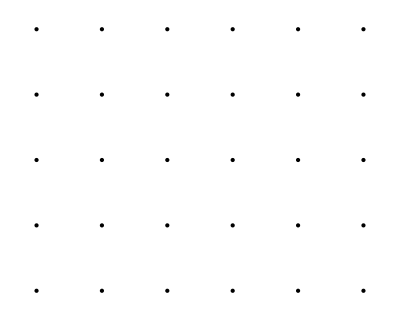

```mathematica
Graphics[Point[{1,2}]]
Graphics[Point[Table[{t*2,0},{t,0,10,1}]]]
T1[jj_]=Table[{i,jj},{i,0,5}]
T=T1[0]
Join[T1[0],T1[1]]
For[j=1,j<=4,j++,T=Join[T,T1[j]]]
T
Graphics[Point[T]]
```